```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
κσr = Last[Flatten[StringSplit[FileNames["KAPPA_SIGMA_R_*",NotebookDirectory[]],"_"]]];
```

/homes/ht/Desktop/analytical_prakash_kappa6

```mathematica
DataPlots=Table[{StringSplit[FileNames["Analysis*"][[i]],"_"][[2]],
path=FileNames["Analysis*"][[i]]<>"/";
ListLinePlot[{Import[path<>"new2_force.data","Table"]},PlotMarkers->{"●"}]},{i,1,Length[FileNames["Analysis*"]]}];
```

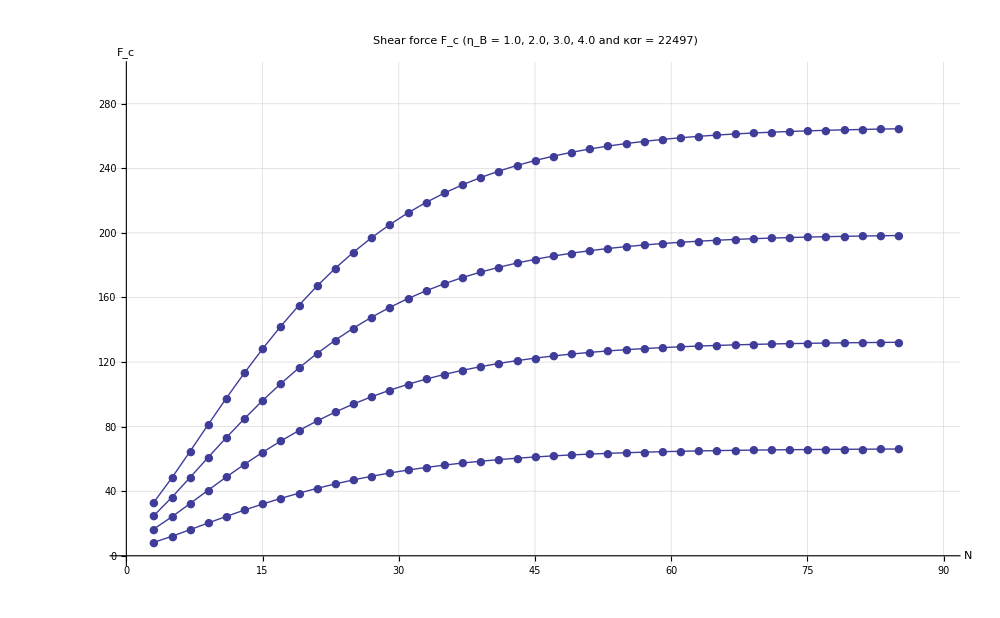

```mathematica
fsTitle=24;
fsAxesLabel=18;
fs2=16;

Show[
{
DataPlots[[1,2]],
DataPlots[[2,2]],
DataPlots[[3,2]],
DataPlots[[4,2]]
},
PlotRange->{{0,90},{0,300}},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
AxesLabel->{
Style["N",FontSize->fsAxesLabel],
Style["F_c",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotLabel->Style["Shear force F_c (η_B = "<>ToString[DataPlots[[1,1]]]<>", " <>ToString[DataPlots[[2,1]]]<>", " <>ToString[DataPlots[[3,1]]]<>", " <>ToString[DataPlots[[4,1]]]<>" and κσr = "<>ToString[κσr]<>")",FontSize->fsTitle],
ImageSize->1000
]
```